# Visualizing RE Results

```mathematica
SetDirectory[$HomeDirectory];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","DialecticalStructures"}]];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","ReflectiveEquilibrium"}]];
<<DialecticalStructures`BasicTDS`;
<<DialecticalStructures`InductiveReasoning`;
<<DialecticalStructures`PositionsAnalytics`;
<<ReflectiveEquilibrium`ReflectiveEquilibrium`;
```

## Visualizing Single Runs

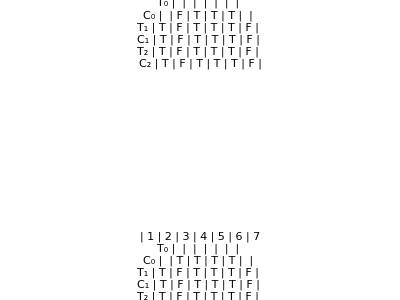

```mathematica
Module[{
ensembleDir="four_cases",
fileRoot="2016_09_08-0001"
},
GraphicsColumn[
Table[
PlotRE[
Get[FileNameJoin[{
NotebookDirectory[],
"..",
"results",
ensembleDir, 
fileRoot<>"#"<>IntegerString[i,10,6]<>".m"
}]]
],
{i,4}
]
]
]
```